```mathematica
(***EN COLOR ROJO*****)
(************************************************)
nred=5; (*número de la red a analizar*)
n=4; (*número de nodos*)
(*********************************)
state=Import[NotebookDirectory[]<>ToString[nred]<>"dinámica_red.txt","Lines"] ;(*abrimos el archivo con la dinámica de la red en cuestión*)
matadyacente=Table[Table[0,2^n],2^n] ;(*inicializamos la matriz adyacente para la cuenca de atractores*)

i=1; (*contador*)
Do[
matadyacente[[i,FromDigits[ToExpression[state[[i]]],2]+1]]=1;
i++
,2^n]
Export[NotebookDirectory[]<>"Cuenca de atractores de la Red "<>ToString[nred]<>".png",AdjacencyGraph[ToExpression[matadyacente],VertexShapeFunction->"Circle", VertexLabels->Table[w->Placed[(w-1),Center],{w,2^n}],VertexSize->0.6,VertexStyle->RGBColor[1,.78,.72],EdgeStyle->Red,EdgeStyle->Arrowheads[Small]],ImageResolution->170];
```

```mathematica
AdjacencyGraph[ToExpression[matadyacente],VertexShapeFunction->"Circle", VertexLabels->Table[w->Placed[(w-1),Center],{w,2^n}],VertexSize->0.6,VertexStyle->RGBColor[1,.78,.72],EdgeStyle->Red,EdgeStyle->Arrowheads[Small],PlotLabel->"Espacio de estados de la Red "<>ToString[nred]]
```

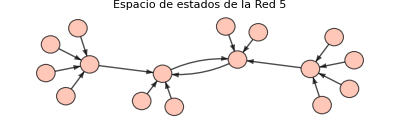

{{1,1,1,1},{0,0,0,1},{0,0,0,0},{1,1,1,0}}

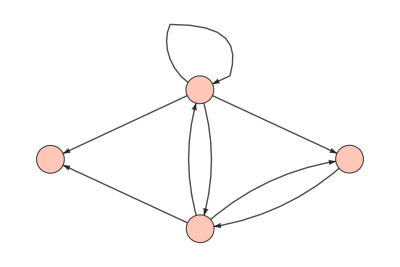

```mathematica
M={{1,1,1,1},{0,0,0,1},{0,0,0,0},{1,1,1,0}}
AdjacencyGraph[M,VertexShapeFunction->"Circle",VertexSize->0.2,VertexLabels->{1->Placed[Style["1",FontSize->24],Center],2->Placed[Style["2",FontSize->24],Center],3->Placed[Style["3",FontSize->24],Center],4->Placed[Style["4",FontSize->24],Center]},VertexStyle->RGBColor[1,.78,.72],EdgeStyle->Black,EdgeStyle->Arrowheads[Small]]
```

```mathematica
Export[NotebookDirectory[]<>"Grafo"<>ToString[5]<>".png",AdjacencyGraph[M,VertexShapeFunction->"Circle",VertexSize->0.2,VertexLabels->{1->Placed[Style["1",FontSize->24],Center],2->Placed[Style["2",FontSize->24],Center],3->Placed[Style["3",FontSize->24],Center],4->Placed[Style["4",FontSize->24],Center]},VertexStyle->RGBColor[1,.78,.72],EdgeStyle->Black,EdgeStyle->Arrowheads[Small]],ImageResolution->170];
```